# Elliptic Curve Picard-Fuchs Analysis

Based on Christian Schnell’s article which analyzes the equation stating in Hesse Form
F(x,y,z) = t(x^3+y^3+z^3)-3 x y z
For fixed  t≠0 this is, up to scaling, the Hesse normal form t(x^3+y^3+z^3)-3 λ x y z, λ=1/t
which is a standard model of an elliptic curve in the plane. Every nonsingular
plane cubic is projectively equivalent to such a Hesse curve.

## Reduction to Normal Form

First we choose and affine  chart where z=1
 t(x^3+y^3+1)-3 x y which is “twisted Hesse” elliptic curve 
 ax^3+y^3+1=dxy with d=3 and a = t.
( https://people.tamu.edu/~rojas//cubic2weierstrass.pdf?utm_source=chatgpt.com)

There is a standard projective algorithm (explained e.g. in
Silverman–Tate or in the notes by Duif on transforming a general cubic to
Weierstrass form) which, roughly, does the following:

Pick a flex point on the cubic and move it to infinity by a linear
change of projective coordinates.
For a Hesse curve this is easy because the flexes are known explicitly;
for the twisted Hessian form (*) one convenient choice is the point
(0,−1) in the affine chart.

Make the tangent at that flex the line at infinity Z=0
After this step, the resulting projective model has exactly one point at
infinity, which will be the group identity on the elliptic curve.

Eliminate mixed terms so that in the new affine chart Z=1 the
equation becomes quadratic in one variable, say

Y^2+a1XY+a3 Y=X^3+a2 X^2+a4 X+a6.
Complete the square in  Y
Y to arrive at

Y^('2)=X^3+AX^2+BX+C

(in characteristic ≠2,3 one can even kill the 
X^2 term and get the short Weierstrass form 
y^2=x^3+Ax+B
Carrying this out with 
F = t(x^3+y^3+1)−3xy
 is straightforward but very
computationally heavy by hand; that’s why Schnell suggests using
Mathematica and so here we are...

```mathematica
Clear[x,y,z,t,L];
F=t (x^3+y^3+z^3)-3 x y z;
P={1,-1,0};

gradP=(Grad[F,{x,y,z}]/. Thread[{x,y,z}->P])//Simplify
L=(gradP.{x,y,z})//Expand//Simplify
Factor[L]
```

{3 t,3 t,3}

3 (t (x+y)+z)

3 (t x+t y+z)

```mathematica
{Coefficient[L,x],Coefficient[L,y],Coefficient[L,z]}//Simplify
```

{3 t,3 t,3}

```mathematica
l1=x;
l2=y;
l3=L;

M={{Coefficient[l1,x],Coefficient[l1,y],Coefficient[l1,z]},{Coefficient[l2,x],Coefficient[l2,y],Coefficient[l2,z]},{Coefficient[l3,x],Coefficient[l3,y],Coefficient[l3,z]}};

Det[M]//Simplify
```

3

```mathematica
Clear[X,Y,Z,Minv,xyzInNew,Fnew,aff];

(*Your linear map is:X=l1=x,Y=l2=y,Z=l3=L=3(t x+t y+z)*)
(*So (X,Y,Z)^T=M.(x,y,z)^T with M as you built.*)

Minv=Inverse[M]//Simplify;

(*express old coordinates in terms of new*)
xyzInNew=Thread[{x,y,z}->(Minv.{X,Y,Z})]//Simplify;

(*substitute into the original cubic and clear denominators*)
Fnew=Expand[F/. xyzInNew]//Simplify;

(*dehomogenize:take affine patch Z=1*)
aff=Expand[Fnew/. Z->1]//Simplify;

aff//Factor
```

1/27 (t-9 t^2 X+27 t^3 X^2+27 t X^3-27 t^4 X^3-9 t^2 Y-27 X Y+54 t^3 X Y+81 t X^2 Y-81 t^4 X^2 Y+27 t^3 Y^2+81 t X Y^2-81 t^4 X Y^2+27 t Y^3-27 t^4 Y^3)

```mathematica
{X,Y,Z}/. Thread[{x,y,z}->P]/. {X->l1,Y->l2,Z->l3}//Simplify
```

{x,y,3 (t (x+y)+z)}

```mathematica
Clear[X,Y,Z,Minv,xyzInNew,Fnew,aff];

(*Your linear map is:X=l1=x,Y=l2=y,Z=l3=L=3(t x+t y+z)*)
(*So (X,Y,Z)^T=M.(x,y,z)^T with M as you built.*)

Minv=Inverse[M]//Simplify;

(*express old coordinates in terms of new*)
xyzInNew=Thread[{x,y,z}->(Minv.{X,Y,Z})]//Simplify;

(*substitute into the original cubic and clear denominators*)
Fnew=Expand[F/. xyzInNew]//Simplify;

(*dehomogenize:take affine patch Z=1*)
aff=Expand[Fnew/. Z->1]//Simplify;

aff//Factor
```

1/27 (t-9 t^2 X+27 t^3 X^2+27 t X^3-27 t^4 X^3-9 t^2 Y-27 X Y+54 t^3 X Y+81 t X^2 Y-81 t^4 X^2 Y+27 t^3 Y^2+81 t X Y^2-81 t^4 X Y^2+27 t Y^3-27 t^4 Y^3)

```mathematica
{X,Y,Z}/. Thread[{x,y,z}->P]/. {X->l1,Y->l2,Z->l3}//Simplify
```

{x,y,3 (t (x+y)+z)}

```mathematica
Clear[X,Y,Z,x1,y1,aff,affH,aff2];

(*paste your aff exactly as you have it*)
aff=1/27 (t-9 t^2 X+27 t^3 X^2+27 t X^3-27 t^4 X^3-9 t^2 Y-27 X Y+54 t^3 X Y+81 t X^2 Y-81 t^4 X^2 Y+27 t^3 Y^2+81 t X Y^2-81 t^4 X Y^2+27 t Y^3-27 t^4 Y^3);
aff2=Expand[27 aff]
```

t-9 t^2 X+27 t^3 X^2+27 t X^3-27 t^4 X^3-9 t^2 Y-27 X Y+54 t^3 X Y+81 t X^2 Y-81 t^4 X^2 Y+27 t^3 Y^2+81 t X Y^2-81 t^4 X Y^2+27 t Y^3-27 t^4 Y^3

```mathematica
Clear[x1,y1];

aff3=Expand[aff2/. {X->y1,Y->x1-y1}]//Factor;

aff3
```

t-9 t^2 x1+27 t^3 x1^2+27 t x1^3-27 t^4 x1^3-27 x1 y1+27 y1^2

```mathematica
Exponent[aff3,y1]
```

2

```mathematica
A=Coefficient[aff3,y1,2]//Simplify;
B=Coefficient[aff3,y1,1]//Simplify;
C0=Coefficient[aff3,y1,0]//Simplify;
```

```mathematica
rhs=Expand[B^2-4 A C0]//Simplify;
```

```mathematica
(2 A y1+B)^2==rhs
```

(-27 x1+54 y1)^2==27 (36 t^2 x1+27 x1^2-108 t^3 x1^2+108 t^4 x1^3-4 t (1+27 x1^3))

```mathematica
yhat=2 A y1+B
```

-27 x1+54 y1

```mathematica
Exponent[rhs,x1]
```

3

```mathematica
target=t x^3
+1/4 (1-4 t^3) x^2
+1/3 t^2 (t^3-1) x
-1/27 t (t^3-1)^2;
```

t x^3

1/4 (1-4 t^3) x^2

1/3 t^2 (-1+t^3) x

```mathematica
rhs
```

27 (36 t^2 x1+27 x1^2-108 t^3 x1^2+108 t^4 x1^3-4 t (1+27 x1^3))

```mathematica
Clear[a,b,c,x,y];

rhsSub=Expand[rhs/. x1->a x+b];
eq=Expand[rhsSub-c^2 target];

sol=FullSimplify[Solve[Thread[CoefficientList[eq,x]=={0,0,0,0}],{a,b,c}],Assumptions->t!=0&&t^3!=1];

sol//Simplify
```

{{a→0,b→(-1+4 t^3+(1+8 t^3)/((-1+20 t^3+8 t^6+8 √(t^3 (-1+t^3)^3))^(1/3))+(-1+20 t^3+8 t^6+8 √(t^3 (-1+t^3)^3))^(1/3))/(12 t (-1+t^3)),c→0},{a→0,b→1/(24 t (-1+t^3))(-2+8 t^3+((-1-ⅈ √3) (1+8 t^3))/((-1+20 t^3+8 t^6+8 √(t^3 (-1+t^3)^3))^(1/3))+ⅈ (ⅈ+√3) (-1+20 t^3+8 t^6+8 √(t^3 (-1+t^3)^3))^(1/3)),c→0},{a→0,b→1/(24 t (-1+t^3))(-2+8 t^3+(ⅈ (ⅈ+√3) (1+8 t^3))/((-1+20 t^3+8 t^6+8 √(t^3 (-1+t^3)^3))^(1/3))-(1+ⅈ √3) (-1+20 t^3+8 t^6+8 √(t^3 (-1+t^3)^3))^(1/3)),c→0}}

## Brute force Picard Fuchs Derivation

```mathematica
ClearAll[x,t,y,B,Cc,Q,Qt,Qtt,P,Ek,a,solA,Rem,solBC];

(*The "normal form" cubic:y^2=Q(x,t)*)
Q=t x^3+(1/4) (1-4 t^3) x^2+(1/3) t^2 (t^3-1) x-(1/27) t (t^3-1)^2;
Qt=D[Q,t];
Qtt=D[Q,{t,2}];

(*Treat y as y(t) for differentiation,then impose y^2=Q via derivative identities:2 y y_t=Q_t 2 y_t^2+2 y y_tt=Q_tt*)
rulesY={y[t]->y,Derivative[1][y][t]->Qt/(2 y),Derivative[2][y][t]->Qtt/(2 y)-Qt^2/(4 y^3)};
(*omega=dx/y,so we track only its coefficient 1/y*)
f0=1/y[t];
f1=D[f0,t]//Simplify;
f2=D[f0,{t,2}]//Simplify;
(*eta=(d^2/dt^2+B d/dt+C) omega=>coefficient times dx*)
etaCoeff=Simplify[(f2+B f1+Cc f0)/. rulesY];

(*Put eta in the form P(x)/y^5 dx by multiplying through by y^5 and using y^2=Q*)
P=Expand[(etaCoeff*y^5)//. y^2->Q//.y^4->Q^2]//Simplify;

(*Exact forms:d(x^k/y^3)=[k x^(k-1) Q-(3/2) x^k Q_x]/y^5 dx (since y_x=Q_x/(2y) and y^2=Q)*)
Qx=D[Q,x];
Ek[k_]:=Expand[k x^(k-1) Q-(3/2) x^k Qx];

(*Solve for a_k so that degrees x^6..x^2 cancel in P-Sum a_k Ek(k)*)
aVars=Array[a,5,0];               (*a[0],...,a[4]*)
expr=Expand[P-Sum[a[k] Ek[k],{k,0,4}]];

eqsA=Table[Coefficient[expr,x,n]==0,{n,2,6}];
solA=Solve[eqsA,aVars][[1]];

Rem=Expand[expr/. solA];         (*should be degree<=1 in x*)

(*Now set remaining two coefficients (x^1 and x^0) to zero to solve for B,C*)
eqsBC={Coefficient[Rem,x,1]==0,Coefficient[Rem,x,0]==0};
solBC=FullSimplify[Solve[eqsBC,{B,Cc}],Assumptions->t!=0&&t^3!=1];

solBC//FullSimplify
```

{{B→(1-4 t^3)/(t-t^4),Cc→(2 t)/(-1+t^3)}}

## Solving the PF system and monodromy

Now we have Picard Fuchs coefficients for periods. Let’s go further and build a	 “elliptic PF → geometry → modular data → monodromy” package

```mathematica
ClearAll[x,t,A2,A4,A6,f,Δ,j];

A2=1/4 (1-4 t^3);
A4=1/3 t^2 (t^3-1);
A6=-1/27 t (t^3-1)^2;

f[x_]:=x^3+A2 x^2+A4 x+A6;
```

```mathematica
Δ=Discriminant[f[x],x]//Factor
```

-1/432 (-1+t)^3 t (1+t+t^2)^3 (1-16 t+24 t^2-8 t^3+16 t^4-32 t^5+16 t^6)

```mathematica
Solve[Δ==0,t] (* singular fibers *)
```

{{t→0},{t→1},{t→1},{t→1},{t→-(-1)^(1/3)},{t→-(-1)^(1/3)},{t→-(-1)^(1/3)},{t→(-1)^(2/3)},{t→(-1)^(2/3)},{t→(-1)^(2/3)},{t→},{t→},{t→},{t→},{t→},{t→}}

```mathematica
a2=A2;a4=A4;a6=A6;

b2=4 a2;
b4=2 a4;
b6=4 a6;

c4=b2^2-24 b4//Simplify;
c6=-b2^3+36 b2 b4-216 b6//Simplify;

ΔWeier=(c4^3-c6^2)/1728//Simplify//Factor;

j=Simplify[c4^3/ΔWeier]//FullSimplify//Factor (* j invariant *)
```

-(27 (1+16 t^2-8 t^3-16 t^5+16 t^6)^3)/((-1+t)^3 t (1+t+t^2)^3 (1-16 t+24 t^2-8 t^3+16 t^4-32 t^5+16 t^6))

```mathematica
ClearAll[t,A2,A4,A6,a2,a4,a6,b2,b4,b6,c4,c6,ΔWeier,j];

(*Schnell’s coefficients in y^2=t x^3+A2 x^2+A4 x+A6*)
A2=1/4 (1-4 t^3);
A4=1/3 t^2 (t^3-1);
A6=-1/27 t (t^3-1)^2;

(*Normalize with X=t x,Y=t y->Y^2=X^3+a2 X^2+a4 X+a6*)
a2=A2;
a4=t A4;
a6=t^2 A6;

b2=4 a2;
b4=2 a4;
b6=4 a6;

c4=Simplify[b2^2-24 b4];
c6=Simplify[-b2^3+36 b2 b4-216 b6];

ΔWeier=Simplify[(c4^3-c6^2)/1728]//Factor;
jInv=FullSimplify[c4^3/ΔWeier]//Factor//FullSimplify;

{ΔWeier,jInv}
```

{-1/27 (-1+t)^3 t^3 (1+t+t^2)^3,-(27 (1+8 t^3)^3)/(t^3 (-1+t^3)^3)}

### Solve the PF in terms of HGF

```mathematica
Bpf=(4 t^3-1)/(t (t^3-1));
Cpf=(2 t)/(t^3-1);
```

```mathematica
ClearAll[u,Φ];

(*chain rule operators*)
dtdU=1/(3 t^2);

(*define substitution*)
uSub=u==t^3;

(*rewrite equation manually*)
Φ[u_]:=Φ[u];   (*dummy*)

(*operator change*)
(*use formula:d/dt=3 t^2 d/du*)
```

```mathematica
Clear[Φ];

(*express Pi[t]=Φ[t^3]*)
Π[t_]:=Φ[t^3];

expr=D[Π[t],{t,2}]+Bpf D[Π[t],t]+Cpf Π[t];

expr2=Simplify[expr/. {D[Φ[t^3],t]->3 t^2 Φ'[t^3],D[Φ[t^3],{t,2}]->6 t Φ'[t^3]+9 t^4 Φ''[t^3]}];

(*divide by 9 t^4 to normalize*)
exprHG=Simplify[expr2/(9 t^4)]
%/. t^3->u
%/. 1/t^3->1/u//Simplify//FullSimplify
exprHGu=%
```

(2 Φ[t^3])/(9 t^3 (-1+t^3))+((-1+2 t^3) Φ'[t^3])/(t^3 (-1+t^3))+Φ''[t^3]

(2 Φ[u])/(9 t^3 (-1+u))+((-1+2 u) Φ'[u])/(t^3 (-1+u))+Φ''[u]

(2 Φ[u]+9 (-1+2 u) Φ'[u])/(9 (-1+u) u)+Φ''[u]

(2 Φ[u]+9 (-1+2 u) Φ'[u])/(9 (-1+u) u)+Φ''[u]

```mathematica
DSolve[exprHGu==0,Φ,u]
```

{{Φ→Function[{u},C[1] LegendreP[-1/3,-1+2 u]+C[2] LegendreQ[-1/3,-1+2 u]]}}

```mathematica
Clear[Y];
(* Gauss Manin connection *)
GM={{0,1},{-Cpf,-Bpf}}//Simplify
```

{{0,1},{-(2 t)/(-1+t^3),-(1-4 t^3)/(t-t^4)}}

```mathematica
ClearAll[ode,sol,t0,ics,loop,solLoop,M0];

ode={y''[t]+Bpf y'[t]+Cpf y[t]==0};
t0=0.05;
ics={y1[t0]==1,y1'[t0]==0,y2[t0]==0,y2'[t0]==1};
```

```mathematica
sol=NDSolve[{y1''[t]+Bpf y1'[t]+Cpf y1[t]==0,y2''[t]+Bpf y2'[t]+Cpf y2[t]==0,y1[t0]==1,y1'[t0]==0,y2[t0]==0,y2'[t0]==1},{y1,y2},{t,t0,0.8},Method->{"StiffnessSwitching"},MaxStepFraction->1/50];
```

```mathematica
loop[θ_]:=t0 Exp[I θ];

solLoop=NDSolve[{y1''[t]+Bpf y1'[t]+Cpf y1[t]==0,y2''[t]+Bpf y2'[t]+Cpf y2[t]==0,y1[t0]==1,y1'[t0]==0,y2[t0]==0,y2'[t0]==1},{y1,y2},{t,t0 Exp[0 I],t0 Exp[2 π I]},Method->{"StiffnessSwitching"}];
```

```mathematica
M0={{y1[t0 Exp[2 π I]]/. solLoop[[1]],y2[t0 Exp[2 π I]]/. solLoop[[1]]},{Derivative[1][y1][t0 Exp[2 π I]]/. solLoop[[1]],Derivative[1][y2][t0 Exp[2 π I]]/. solLoop[[1]]}}//N
```

{{1.,0.},{0.,1.}}

```mathematica
sol
```

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

```mathematica
solHG=DSolve[u (1-u) Φ''[u]+(1-2 u) Φ'[u]-2/9 Φ[u]==0,Φ[u],u]
```

{{Φ[u]→C[1] LegendreP[-1/3,-1+2 u]+C[2] LegendreQ[-1/3,-1+2 u]}}

```mathematica
FullSimplify[LegendreP[-1/3,2 u-1],FunctionExpand]
```

LegendreP[-1/3,-1+2 u]

```mathematica
ClearAll[t,θ,t0,Bpf,Cpf,A,tpath,eqs,solY,Y11,Y12,Y21,Y22,M0];

Bpf[t_]:=(4 t^3-1)/(t (t^3-1));
Cpf[t_]:=(2 t)/(t^3-1);

A[t_]:={{0,1},{-Cpf[t],-Bpf[t]}};

(*loop around t=0*)
t0=0.05;
tpath[θ_]:=t0 Exp[I θ];
tprime[θ_]:=D[tpath[θ],θ];

(*unknown fundamental matrix entries*)
eqs={Y11'[θ]==tprime[θ] (A[tpath[θ]].{{Y11[θ],Y12[θ]},{Y21[θ],Y22[θ]}})[[1,1]],Y12'[θ]==tprime[θ] (A[tpath[θ]].{{Y11[θ],Y12[θ]},{Y21[θ],Y22[θ]}})[[1,2]],Y21'[θ]==tprime[θ] (A[tpath[θ]].{{Y11[θ],Y12[θ]},{Y21[θ],Y22[θ]}})[[2,1]],Y22'[θ]==tprime[θ] (A[tpath[θ]].{{Y11[θ],Y12[θ]},{Y21[θ],Y22[θ]}})[[2,2]],(*start with identity at θ=0*)Y11[0]==1;Y12[0]==0;
Y21[0]==0;Y22[0]==1};

solY=NDSolve[eqs,{Y11,Y12,Y21,Y22},{θ,0,2 Pi},Method->{"StiffnessSwitching"},MaxStepFraction->1/200,WorkingPrecision->50,AccuracyGoal->50,PrecisionGoal->50][[1]];

M0={{Y11[2 Pi],Y12[2 Pi]},{Y21[2 Pi],Y22[2 Pi]}}/. solY//N[#,50]&
```

NDSolve::precw: The precision of the differential equation ({{Y11'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) Y21[θ],Y12'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) Y22[θ],Y21'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) (-(0.1 ⅇ^Times[«2»] Y11[θ])/Plus[«2»]-(20. ⅇ^Times[«2»] (-1+Times[«2»]) Y21[θ])/Plus[«2»]),Y22'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) (-(0.1 ⅇ^Times[«2»] Y12[θ])/Plus[«2»]-(20. ⅇ^Times[«2»] (-1+Times[«2»]) Y22[θ])/Plus[«2»]),Y22[0]==1},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndnco: The number of constraints (1) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (4).

ReplaceAll::reps: {Y11'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) Y21[θ],Y12'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) Y22[θ],Y21'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) (-(0.1 ⅇ^(ⅈ θ) Y11[θ])/(-1+Times[«2»])-(20. ⅇ^(-ⅈ θ) (-1+«22» Power[«1»]) Y21[θ])/(-1+Times[«2»])),Y22'[θ]==(0.+0.05 ⅈ) ⅇ^(ⅈ θ) (-(0.1 ⅇ^(ⅈ θ) Y12[θ])/(-1+Times[«2»])-(20. ⅇ^(-ⅈ θ) (-1+0.0005 Power[«2»]) Y22[θ])/(-1+Times[«2»])),Y22[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Y11'[θ]==(0.+0.05 ⅈ) 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) Y21[θ],Y12'[θ]==(0.+0.05 ⅈ) («83»)^((0.+1. ⅈ) θ) Y22[θ],«1»==«1»,Y22'[θ]==(0.+0.05 ⅈ) («83»)^((«1»)«1»«1») (-(0.1 («83»)^((«1») θ) Y12[θ])/(-1.+Times[«2»])-(«1»)/(-1.+«1»)),Y22[0]==1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{Y11[6.2831853071795864769252867665590057683943387987502],Y12[6.2831853071795864769252867665590057683943387987502]},{Y21[6.2831853071795864769252867665590057683943387987502],Y22[6.2831853071795864769252867665590057683943387987502]}}/.{Y11'[θ]==(0.+0.05 ⅈ) 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) Y21[θ],Y12'[θ]==(0.+0.05 ⅈ) 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) Y22[θ],Y21'[θ]==(0.+0.05 ⅈ) 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) (-((0.1 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) Y11[θ])/(-1.+0.000125 2.7182818284590452353602874713526624977572470937^((0.+3. ⅈ) θ)))-(20. 2.7182818284590452353602874713526624977572470937^((0.-1. ⅈ) θ) (-1.+0.0005 2.7182818284590452353602874713526624977572470937^((0.+3. ⅈ) θ)) Y21[θ])/(-1.+0.000125 2.7182818284590452353602874713526624977572470937^((0.+3. ⅈ) θ))),Y22'[θ]==(0.+0.05 ⅈ) 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) (-((0.1 2.7182818284590452353602874713526624977572470937^((0.+1. ⅈ) θ) Y12[θ])/(-1.+0.000125 2.7182818284590452353602874713526624977572470937^((0.+3. ⅈ) θ)))-(20. 2.7182818284590452353602874713526624977572470937^((0.-1. ⅈ) θ) (-1.+0.0005 2.7182818284590452353602874713526624977572470937^((0.+3. ⅈ) θ)) Y22[θ])/(-1.+0.000125 2.7182818284590452353602874713526624977572470937^((0.+3. ⅈ) θ))),Y22[0]==1.}

## Modular Invariants

```mathematica
ClearAll[t,u,x,ν,Pi1,Pi2,tau];

u[t_]:=t^3;
x[t_]:=2 u[t]-1;          (*x=2u-1 maps u=0,1,∞ to x=-1,1,∞*)
ν=-1/3;

(*Two independent local solutions of the PF equation in u-variable*)
Pi1[t_]:=LegendreP[ν,x[t]];
Pi2[t_]:=LegendreQ[ν,x[t]];

tau[t_]:=Pi2[t]/Pi1[t];
```

```mathematica
ClearAll[tauN];
tauN[t_?NumericQ,eps_:10^-10]:=Module[{tt=t+I eps},N[tau[tt],50]];
```

```mathematica
tauN[0.2]
tauN[0.4]
tauN[0.8]
```

-0.0965565+1.50369×10^-10 ⅈ

0.18823+1.41837×10^-10 ⅈ

0.924839+2.88535×10^-10 ⅈ

```mathematica
ClearAll[jt,jFromTau];
jt[t_]:=27 (1+8 t^3)^3/(t^3 (1-t^3)^3);

jFromTau[t_?NumericQ]:=Module[{τ=tauN[t]},N[ModularJ[τ],30]];

{jt[0.2]//N[#,30]&,jFromTau[0.2]}
```

{4164.51,ModularJ[-0.0965565+1.50369×10^-10 ⅈ]}

```mathematica
(* Mathematica has various builtins for the J invariant *)
```

```mathematica
ClearAll[q,theta2,theta3,theta4,jTheta];
q[τ_]:=Exp[Pi I τ];
theta2[τ_]:=EllipticTheta[2,0,q[τ]];
theta3[τ_]:=EllipticTheta[3,0,q[τ]];
theta4[τ_]:=EllipticTheta[4,0,q[τ]];

(*modular lambda and j(lambda)*)
lambda[τ_]:=(theta2[τ]^4)/(theta3[τ]^4);
jTheta[τ_]:=256 (1-lambda[τ]+lambda[τ]^2)^3/(lambda[τ]^2 (1-lambda[τ])^2);

jFromTau2[t_?NumericQ]:=Module[{τ=tauN[t]},N[jTheta[τ],30]];

{jt[tauN[0.2]]//N[#,30]&,jFromTau2[0.2]}
```

{-29270.4-0.000140095 ⅈ,-2.70933×10^6+2.49665×10^7 ⅈ}

```mathematica
xλ[τ_]:=ModularLambda[τ](1-ModularLambda[τ])
jλ[τ_]:=256 (1-xλ[τ])^3/xλ[τ]^2
```

```mathematica
jλ[tauN[.2]]//N
KleinInvariantJ[tauN[.2]]*1728 (* need to multiply by 1728 *)
```

-2.70934×10^6+2.49666×10^7 ⅈ

-2.70934×10^6+2.49666×10^7 ⅈ

```mathematica
tauN[.2]
```

LegendreQ[-0.33333333333333333333333333333333333333333333333333,x[0.2+1.×10^-10 ⅈ]]/LegendreP[-0.33333333333333333333333333333333333333333333333333,x[0.2+1.×10^-10 ⅈ]]

```mathematica
ClearAll[tauUpper];
tauUpper[t_?NumericQ,eps_:10^-10]:=Module[{τ=tauN[t,eps]},If[Im[τ]<0,-Conjugate[τ],τ]];
```

```mathematica
tauUpper[.05]
```

-0.37122+2.61688×10^-10 ⅈ

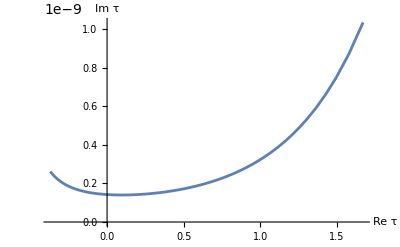

```mathematica
pts=Table[tauUpper[s],{s,0.05,0.95,0.01}];
ListLinePlot[{ReIm/@pts},PlotRange->All,AxesLabel->{"Re τ","Im τ"}]
```

```mathematica
ClearAll[t,x,Q,roots,ω1,ω2,tauPeriod,jt,jFromTau];

Q[x_,t_]:=t x^3+(1/4) (1-4 t^3) x^2+(1/3) t^2 (t^3-1) x-(1/27) t (t^3-1)^2;

(*your rational j(t)*)
jt[t_]:=27 (1+8 t^3)^3/(t^3 (1-t^3)^3);

(*period ratio from branch-cut integrals*)
tauPeriod[t_?NumericQ]:=Module[{rr,e1,e2,e3,w1,w2},rr=Sort[x/. NSolve[Q[x,t]==0,x,WorkingPrecision->50]];
{e1,e2,e3}=rr;
(*ω1:real period over[e2,e3] where Q>=0*)w1=2 NIntegrate[1/Sqrt[Q[x,t]],{x,e2,e3},WorkingPrecision->50,AccuracyGoal->50,PrecisionGoal->50,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
(*ω2:second period over[e1,e2];here Q<=0,so sqrt picks up i*)w2=2 NIntegrate[1/Sqrt[Q[x,t]],{x,e1,e2},WorkingPrecision->50,AccuracyGoal->50,PrecisionGoal->50,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
w2/w1];

(*modular j from τ (Mathematica convention:KleinInvariantJ gives j/1728)*)
jFromTau[t_?NumericQ]:=Module[{τ=tauPeriod[t]},1728 KleinInvariantJ[τ]];

(*test at a few points*)
Table[{tt,N[jt[tt],30],N[jFromTau[tt],30],N[jFromTau[tt]/jt[tt],20]},{tt,{2/10,4/10,6/10,8/10}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.1572913574327261221813633684220374925657018228706541934318304808921299363224729167676147083171325323}. NIntegrate obtained 4.574454564478130893748814337035857709547976747931896417450421195719232924037869959724669124652103484×10^-32-6.294405335581528215495700511182673070378451761963941222303584308066764127604936428761174618113905683 ⅈ and 3.68545173848336226510767691756207416931365088385809182294613139523497950510131176459720541082223669×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-1.239631389636361253808384178639975869391128337011045307623884931108057463491405016235984178945042103}. NIntegrate obtained 8.134190991431398432749233051483079743872501356827239569574437483711119734159810068345752812413835759-1.140133022551179868871972357626313621166061462872879523401251980104364093506092450627633247149113289×10^-31 ⅈ and 3.21017313055083788927308624408194486362216939013241877399983216588837902195716704516582772955949549×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.1572913574327261221813633684220374925657018228706541934318304808921299363224729167676147083171325323}. NIntegrate obtained 4.574454564478130893748814337035857709547976747931896417450421195719232924037869959724669124652103484×10^-32-6.294405335581528215495700511182673070378451761963941222303584308066764127604936428761174618113905683 ⅈ and 3.68545173848336226510767691756207416931365088385809182294613139523497950510131176459720541082223669×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{1/5,4164.50746188026585210298412272,4164.50746188026585210298411652+0. ⅈ,1.+0. ⅈ},{2/5,1778.32697997269003186162949477,1778.32697997269003186265798559+0. ⅈ,1.+0. ⅈ},{3/5,5266.17058474785166044760261456,5266.17058474785166044760262863+1.×10^-25 ⅈ,1.+0. ⅈ},{4/5,60051.3251160752441834338556972,60051.3251160752441837239436325+0. ⅈ,1.+0. ⅈ}}

## Residue Method

```mathematica
ClearAll[x,y,z,t,F,s3,Fx,Fy,Fz,vars,gbFull,decomposeFull];

F=t (x^3+y^3+z^3)-3 x y z;
s3=x^3+y^3+z^3;

Fx=D[F,x];Fy=D[F,y];Fz=D[F,z];

vars={x,y,z};

(*Gröbner basis in Q(t)[x,y,z]*)
gbFull=GroebnerBasis[{F,Fx,Fy,Fz},vars,CoefficientDomain->RationalFunctions,MonomialOrder->Lexicographic];

(*reduce by the Gröbner basis (THIS is the ideal remainder)*)
decomposeFull[poly_]:=PolynomialReduce[poly,gbFull,vars,CoefficientDomain->RationalFunctions,MonomialOrder->Lexicographic];
```

```mathematica
{q,rem}=decomposeFull[s3^2];
rem//Factor
```

0

```mathematica
q
```

{z^2,5 t x^2 y+3 y^2 z,0,-3 x^3-y^3,-(x^3 y)/t-5 x^2 z^2,0,x^4/t}

```mathematica
x Fx+y Fy + z Fz == 3 F //FullSimplify
```

True

```mathematica
ClearAll[x,y,z,t,F,Fx,Fy,Fz,vars,gbJ,ModJ];

F=t (x^3+y^3+z^3)-3 x y z;
Fx=D[F,x];Fy=D[F,y];Fz=D[F,z];

vars={x,y,z};

(*Gröbner basis for the Jacobian ideal J= <Fx,Fy,Fz>over Q(t)*)
gbJ=GroebnerBasis[{Fx,Fy,Fz},vars,CoefficientDomain->RationalFunctions,MonomialOrder->Lexicographic];

(*Normal form modulo the Jacobian ideal*)
ModJ[poly_]:=Module[{q,r},{q,r}=PolynomialReduce[poly,gbJ,vars,CoefficientDomain->RationalFunctions,MonomialOrder->Lexicographic];
r//Factor];
```

```mathematica
ModJ[x y z]
ModJ[x^3+y^3+z^3]
```

t z^3

3 z^3

```mathematica
ModJ[Fx]    (*0*)
ModJ[Fy]    (*0*)
ModJ[Fz]    (*0*)

ModJ[(x^3+y^3+z^3)^2]   (*should be 0 “generically” in t,but may need localization*)
```

0

0

0

«1 more identical outputs»

```mathematica
s3=x^3+y^3+z^3;

alphaOf[P_]:=Module[{r=Expand[ModJ[P]],a},(*r should be proportional to s3*)a=FullSimplify[Coefficient[r,x^3]/Coefficient[s3,x^3],Assumptions->t!=0&&t^3!=1];
a];
```

```mathematica
rulesJ={y z->t x^2,x z->t y^2,x y->t z^2};

ModJFast[poly_]:=FixedPoint[Expand[#/. rulesJ]&,Expand[poly]]//Factor;
```

```mathematica
ModJFast[F]
```

-t (2 x^3-y^3-z^3)